```mathematica
ArcCurvature[{x,x^2},x]==ArcCurvature[Normalize@{x,x^2},x]
```

2/((1+4 x^2)^(3/2))==Abs[x]^3 (1+Abs[x]^2)^(3/2) √((2 Abs[x]+4 Abs[x]^3+2 Abs[x]^5-2 x Abs'[x]-6 x Abs[x]^2 Abs'[x]-4 x Abs[x]^4 Abs'[x]+3 x^2 Abs[x] Abs'[x]^2+2 x^2 Abs[x]^3 Abs'[x]^2+x^2 Abs''[x]+3 x^2 Abs[x]^2 Abs''[x]+2 x^2 Abs[x]^4 Abs''[x])^2/(Abs[x]^2+4 x^2 Abs[x]^2+2 Abs[x]^4+8 x^2 Abs[x]^4+Abs[x]^6+4 x^2 Abs[x]^6-2 x Abs[x] Abs'[x]-4 x^3 Abs[x] Abs'[x]-6 x Abs[x]^3 Abs'[x]-12 x^3 Abs[x]^3 Abs'[x]-4 x Abs[x]^5 Abs'[x]-8 x^3 Abs[x]^5 Abs'[x]+x^2 Abs'[x]^2+x^4 Abs'[x]^2+4 x^2 Abs[x]^2 Abs'[x]^2+4 x^4 Abs[x]^2 Abs'[x]^2+4 x^2 Abs[x]^4 Abs'[x]^2+4 x^4 Abs[x]^4 Abs'[x]^2)^3)

```mathematica
FullSimplify[ArcCurvature[{x,x^2},x]==ArcCurvature[Normalize@{x,x^2},x],x∈Reals]
```

$Aborted

```mathematica
Gradient[{x,x^2}]
```

∇{x,x^2}

```mathematica
Grad[{x,x^2},x]
```

{x,x^2}x

```mathematica
Grad[x^2+y^2,{x,y}]
```

{2 x,2 y}

```mathematica
Solve[{2 x==0,2 y==0},{x,y}]
```

{{x→0,y→0}}

```mathematica
Integrate[Sin[x]/x,{x,-∞,∞}]
```

π

```mathematica
Sin[x]/x
```

Sin[x]/x

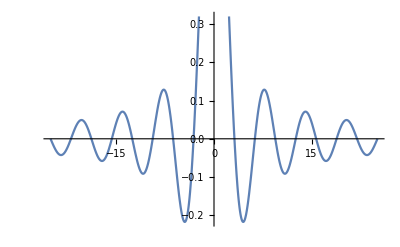

```mathematica
Plot[Sin[x]/x,{x,-25.132741228718345,25.132741228718345}]
```

```mathematica
Roots[Sin[x]/x,x]
```

Roots::eqn: Sin[x]/x is not an equation.

Roots[Sin[x]/x,x]

```mathematica
Roots[Sin[x]/x==0,x]
```

Roots::neq: Sin[x] is expected to be a polynomial in the variable x.

Roots[Sin[x]/x==0,x]

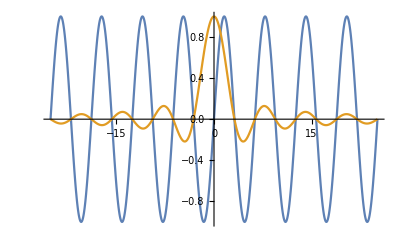

```mathematica
Plot[{Sin[x],Sin[x]/x},{x,-25.132741228718345,25.132741228718345}]
```

```mathematica
Sin[π/2]
```

1

```mathematica
Sin[π/4]
```

1/(√2)

```mathematica
Sin[π]
```

0

```mathematica
Sin[-π]
```

0

```mathematica
Sin[π]/π
```

0

```mathematica
Sin[-π]/-π
```

0

```mathematica
Integrate[Sin[x]/x,{x,-π,π}]
```

2 SinIntegral[π]

```mathematica
N[2 SinIntegral[π]]
```

3.70387

```mathematica
Sin[-2π]
```

0

```mathematica
Integrate[Sin[x]/x,{x,π,2π}]
```

-SinIntegral[π]+SinIntegral[2 π]

```mathematica
Integrate[Sin[x]/x,{x,-π,π}]-2Integrate[Sin[x]/x,{x,π,2π}]
```

2 SinIntegral[π]-2 (-SinIntegral[π]+SinIntegral[2 π])

```mathematica
Distribute[2 SinIntegral[π]-2 (-SinIntegral[π]+SinIntegral[2 π])]
```

2 SinIntegral[π]-2 (-SinIntegral[π]+SinIntegral[2 π])

```mathematica
ExpandAll[2 SinIntegral[π]-2 (-SinIntegral[π]+SinIntegral[2 π])]
```

4 SinIntegral[π]-2 SinIntegral[2 π]

```mathematica
N[4 SinIntegral[π]-2 SinIntegral[2 π]]
```

4.57145

```mathematica
Integrate[Sin[x]/x,{x,-π,π}]+2Integrate[Sin[x]/x,{x,π,2π}]
```

2 SinIntegral[π]+2 (-SinIntegral[π]+SinIntegral[2 π])

```mathematica
ExpandAll[Integrate[Sin[x]/x,{x,-π,π}]+2Integrate[Sin[x]/x,{x,π,2π}]]
```

2 SinIntegral[2 π]

```mathematica
N[2 SinIntegral[2 π]]
```

2.8363

```mathematica
ExpandAll[Integrate[Sin[x]/x,{x,-π,π}]+2Integrate[Sin[x]/x,{x,π,2π}]+2Integrate[Sin[x]/x,{x,2π,3π}]]
```

2 SinIntegral[3 π]

```mathematica
N[2 SinIntegral[3 π]]
```

3.34952

```mathematica
Integrate[Sin[x]/x,{x,-π,π}]+Sum[2Integrate[Sin[x]/x,{x,i π,(i+1)π}],{i,1,2,1}]
```

2 SinIntegral[π]+2 (-SinIntegral[π]+SinIntegral[2 π])+2 (-SinIntegral[2 π]+SinIntegral[3 π])

```mathematica
HoldAll[Integrate[Sin[x]/x,{x,-π,π}]+Sum[2Integrate[Sin[x]/x,{x,i π,(i+1)π}],{i,1,2,1}]]
```

HoldAll[2 SinIntegral[π]+2 (-SinIntegral[π]+SinIntegral[2 π])+2 (-SinIntegral[2 π]+SinIntegral[3 π])]

```mathematica
HoldAll[Integrate[Sin[x]/x,{x,-π,π}]+HoldAll[Sum[2Integrate[Sin[x]/x,{x,i π,(i+1)π}],{i,1,2,1}]]]
```

HoldAll[HoldAll[2 (-SinIntegral[π]+SinIntegral[2 π])+2 (-SinIntegral[2 π]+SinIntegral[3 π])]+2 SinIntegral[π]]

```mathematica
ExpandAll[Integrate[Sin[x]/x,{x,-π,π}]+Sum[2Integrate[Sin[x]/x,{x,i π,(i+1)π}],{i,1,2,1}]]
```

2 SinIntegral[3 π]

```mathematica
ExpandAll[Integrate[Sin[x]/x,{x,-π,π}]+Sum[2Integrate[Sin[x]/x,{x,i π,(i+1)π}],{i,1,5,1}]]
```

2 SinIntegral[6 π]

```mathematica
ExpandAll[Integrate[Sin[x]/x,{x,-π,π}]+Sum[2Integrate[Sin[x]/x,{x,i π,(i+1)π}],{i,1,10,1}]]
```

2 SinIntegral[11 π]

```mathematica
SinIntegral[x]
```

SinIntegral[x]

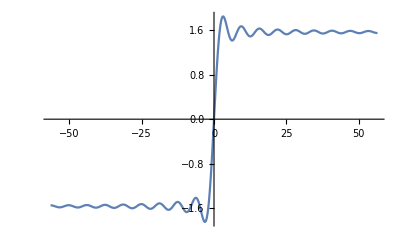

```mathematica
Plot[SinIntegral[x],{x,-56.548667764616276,56.548667764616276}]
```

```mathematica
ExpandAll[Integrate[Sin[x]/x,{x,-π,π}]+Sum[2Integrate[Sin[x]/x,{x,i π,(i+1)π}],{i,1,n,1}]]==2 SinIntegral[(n+1)π]
```

2 SinIntegral[π+n π]==2 SinIntegral[(1+n) π]

```mathematica
FullSimplify[ExpandAll[Integrate[Sin[x]/x,{x,-π,π}]+Sum[2Integrate[Sin[x]/x,{x,i π,(i+1)π}],{i,1,n,1}]]==2 SinIntegral[(n+1)π],n∈]
```

True

```mathematica
Integrate[Sin[x]/x,x]
```

SinIntegral[x]

```mathematica
SinIntegral[x]
```

SinIntegral[x]

```mathematica
Plot[SinIntegral[x],{x,-56.548667764616276,56.548667764616276}]
```

-Graphics-

```mathematica
Limit[SinIntegral[x],x->Infinity]
```

π/2

```mathematica
FullSimplify[ArcCurvature[{x,f[x]},x]==(1+Cos[π x])/2,{x,f[x],f'[x],f''[x]}∈Reals]
```

(1+Cos[π x]) (1+f'[x]^2)^(3/2)==2 Abs[f''[x]]

```mathematica
DSolve[(1+Cos[π x]) (1+f'[x]^2)^(3/2)==2 Abs[f''[x]],{f[x],f[x]},{x}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

$Aborted

```mathematica
Reduce[(1+Cos[π x]) (1+f'[x]^2)^(3/2)==2 Abs[f''[x]]]
```

$Aborted

```mathematica
Reduce[(1+Cos[π x]) (1+f'[x]^2)^(3/2)==2 Abs[f''[x]],x,Reals]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[(1+Cos[π x]) (1+f'[x]^2)^(3/2)==2 Abs[f''[x]],x,ℝ]

```mathematica
Reduce[(1+Cos[π x]) (1+f'[x]^2)^(3/2)==2 Abs[f''[x]],f[x],Reals]
```

Abs[f''[x]]==1/2 (√(1+f'[x]^2)+Cos[π x] √(1+f'[x]^2)+f'[x]^2 √(1+f'[x]^2)+Cos[π x] f'[x]^2 √(1+f'[x]^2))

```mathematica
DSolve[Abs[f''[x]]==1/2 (√(1+f'[x]^2)+Cos[π x] √(1+f'[x]^2)+f'[x]^2 √(1+f'[x]^2)+Cos[π x] f'[x]^2 √(1+f'[x]^2)),{f[x],f[x]},{x}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

$Aborted

```mathematica
Solve[(1+Cos[π x]) (1+f'[x]^2)^(3/2)==2 Abs[f''[x]],f'[x]]
```

{{f'[x]→-√(-1+(4 Abs[f''[x]]^(2/3) Cos[(π x)/2]^(8/3))/(1+2 Cos[π x]+Cos[π x]^2))},{f'[x]→√(-1+(4 Abs[f''[x]]^(2/3) Cos[(π x)/2]^(8/3))/(1+2 Cos[π x]+Cos[π x]^2))},{f'[x]→-√(-1-(2 Abs[f''[x]]^(2/3) Cos[(π x)/2]^(8/3))/(1+2 Cos[π x]+Cos[π x]^2)-(2 ⅈ √3 Abs[f''[x]]^(2/3) Cos[(π x)/2]^(8/3))/(1+2 Cos[π x]+Cos[π x]^2))},{f'[x]→√(-1-(2 Abs[f''[x]]^(2/3) Cos[(π x)/2]^(8/3))/(1+2 Cos[π x]+Cos[π x]^2)-(2 ⅈ √3 Abs[f''[x]]^(2/3) Cos[(π x)/2]^(8/3))/(1+2 Cos[π x]+Cos[π x]^2))},{f'[x]→-√(-1-(2 Abs[f''[x]]^(2/3) Cos[(π x)/2]^(8/3))/(1+2 Cos[π x]+Cos[π x]^2)+(2 ⅈ √3 Abs[f''[x]]^(2/3) Cos[(π x)/2]^(8/3))/(1+2 Cos[π x]+Cos[π x]^2))},{f'[x]→√(-1-(2 Abs[f''[x]]^(2/3) Cos[(π x)/2]^(8/3))/(1+2 Cos[π x]+Cos[π x]^2)+(2 ⅈ √3 Abs[f''[x]]^(2/3) Cos[(π x)/2]^(8/3))/(1+2 Cos[π x]+Cos[π x]^2))}}

```mathematica
Solve[(1+Cos[π x]) (1+f'[x]^2)^(3/2)==2 Abs[f''[x]],f'[x],Reals]
```

{{f'[x]→ConditionalExpression[-√Root[1-4 Abs[f''[x]]^2+2 Cos[π x]+Cos[π x]^2+(3+6 Cos[π x]+3 Cos[π x]^2) #1+(3+6 Cos[π x]+3 Cos[π x]^2) #1^2+(1+2 Cos[π x]+Cos[π x]^2) #1^3&,1],(-1<Cos[π x]<-1+2 Abs[f''[x]]&&Abs[f''[x]]>0)||(-1+2 Abs[f''[x]]<Cos[π x]<-1&&Abs[f''[x]]<0)]},{f'[x]→ConditionalExpression[√Root[1-4 Abs[f''[x]]^2+2 Cos[π x]+Cos[π x]^2+(3+6 Cos[π x]+3 Cos[π x]^2) #1+(3+6 Cos[π x]+3 Cos[π x]^2) #1^2+(1+2 Cos[π x]+Cos[π x]^2) #1^3&,1],(-1<Cos[π x]<-1+2 Abs[f''[x]]&&Abs[f''[x]]>0)||(-1+2 Abs[f''[x]]<Cos[π x]<-1&&Abs[f''[x]]<0)]}}

```mathematica
Integrate[√(-1+(4 Abs[f''[x]]^(2/3) Cos[(π x)/2]^(8/3))/(1+2 Cos[π x]+Cos[π x]^2)),x]
```

∫√(-1+(4 Abs[f''[x]]^(2/3) Cos[(π x)/2]^(8/3))/(1+2 Cos[π x]+Cos[π x]^2))ⅆx

```mathematica
ListPlot@
Table[{i,NIntegrate[√(-1+(4 Abs[f''[x]]^(2/3) Cos[(π x)/2]^(8/3))/(1+2 Cos[π x]+Cos[π x]^2)),{x,0,i}]},{i,1,100,1}]
```

NIntegrate::inumr: The integrand √(-1+(4 Abs[f''[x]]^(2/3) Cos[(π x)/2]^(8/3))/(1+2 Cos[Times[«2»]]+Cos[Times[«2»]]^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand √(-1+(4 Abs[f''[x]]^(2/3) Cos[(π x)/2]^(8/3))/(1+2 Cos[Times[«2»]]+Cos[Times[«2»]]^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,2}}.

NIntegrate::inumr: The integrand √(-1+(4 Abs[f''[x]]^(2/3) Cos[(π x)/2]^(8/3))/(1+2 Cos[Times[«2»]]+Cos[Times[«2»]]^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::nlim: x = i is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

$Aborted

```mathematica
Sin[x y]==0
```

Sin[x y]==0

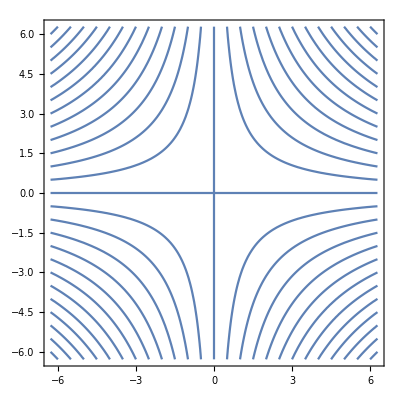

```mathematica
ContourPlot[Sin[x y]==0,{x,-2π,2π},{y,-2π,2π}]
```

```mathematica
Sin[x y]
```

Sin[x y]

```mathematica
Plot3D[Sin[x y],{x,-2.870040244616469,11.33715844542981},{y,-2.869757489945979,11.325565235881088}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,y}∈Disk[]]
```

-Graphics3D-

```mathematica
Manipulate[
ContourPlot[Sin[x y]==n,{x,-2π,2π},{y,-2π,2π}]
,{n,-10,10,1}]
```

```mathematica
Manipulate[
ContourPlot[Sin[x y]==n,{x,-2π,2π},{y,-2π,2π}]
,{n,-1,1,.01}]
```

```mathematica
Grad[Sin[x y]]
```

Grad::argtu: Grad called with 1 argument; 2 or 3 arguments are expected.

Grad[Sin[x y]]

```mathematica
Grad[Sin[x y],{x,y}]
```

{y Cos[x y],x Cos[x y]}

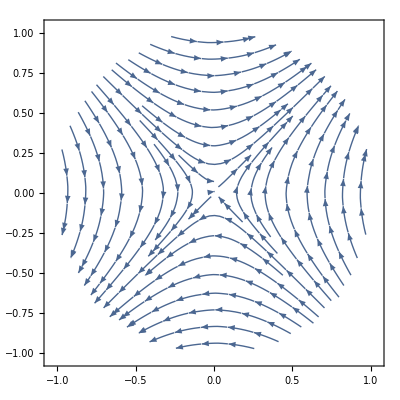

```mathematica
StreamPlot[{y Cos[x y],x Cos[x y]},{x,y}∈Disk[]]
```

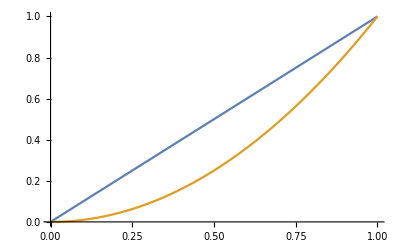

```mathematica
Plot[{x,x^2},{x,0,1}]
```

```mathematica
FullSimplify[ArcCurvature[{x,x^2},x],x∈Reals]
```

2/((1+4 x^2)^(3/2))

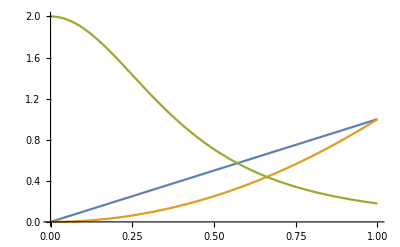

```mathematica
Plot[{x,x^2,2/((1+4 x^2)^(3/2))},{x,0,1}]
```

```mathematica
FullSimplify[Normalize[{x,x}].Normalize[{x,x^2}],x∈Reals]
```

(1+x)/(√2 √(1+x^2))

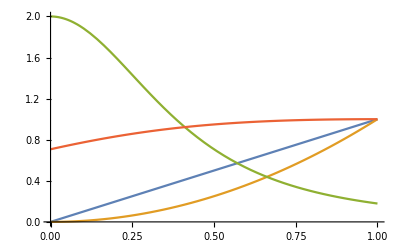

```mathematica
Plot[{x,x^2,2/((1+4 x^2)^(3/2)),(1+x)/(√2 √(1+x^2))},{x,0,1}]
```

```mathematica
Integrate[√(1+4 x^2),x]
```

1/2 x √(1+4 x^2)+1/4 ArcSinh[2 x]

```mathematica
FullSimplify[Integrate[√(1+4 x^2),x],x∈Reals]
```

1/4 (2 x √(1+4 x^2)+ArcSinh[2 x])

```mathematica
Integrate[√(1+1),x]
```

√2 x

```mathematica
(1/4 (2 x √(1+4 x^2)+ArcSinh[2 x]))/(√2 x)
```

(2 x √(1+4 x^2)+ArcSinh[2 x])/(4 √2 x)

```mathematica
FullSimplify[(1/4 (2 x √(1+4 x^2)+ArcSinh[2 x]))/(√2 x),x∈Reals]
```

(2 x √(1+4 x^2)+ArcSinh[2 x])/(4 √2 x)

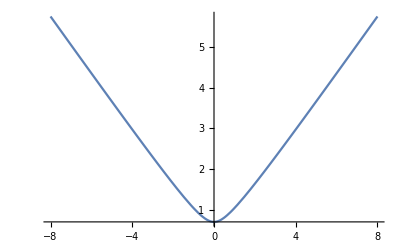

```mathematica
Plot[(2 x √(1+4 x^2)+ArcSinh[2 x])/(4 √2 x),{x,-8,8}]
```

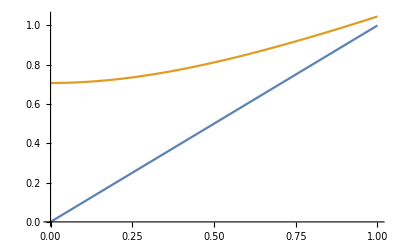

```mathematica
Plot[{x,(2 x √(1+4 x^2)+ArcSinh[2 x])/(4 √2 x)},{x,0,1}]
```

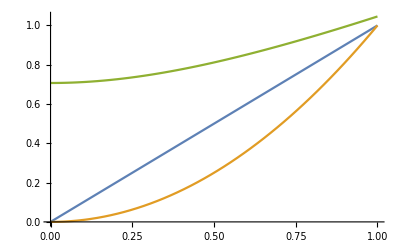

```mathematica
Plot[{x,x^2,(2 x √(1+4 x^2)+ArcSinh[2 x])/(4 √2 x)},{x,0,1}]
```

```mathematica
FullSimplify[1/4 (2 x √(1+4 x^2)+ArcSinh[2 x])-√2 x,x∈Reals]
```

1/4 (-4 √2 x+2 x √(1+4 x^2)+ArcSinh[2 x])

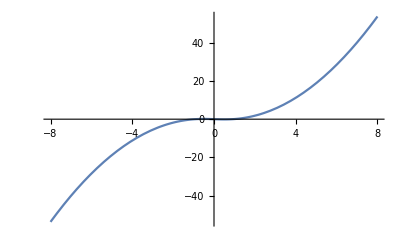

```mathematica
Plot[1/4 (-4 √2 x+2 x √(1+4 x^2)+ArcSinh[2 x]),{x,-8,8}]
```

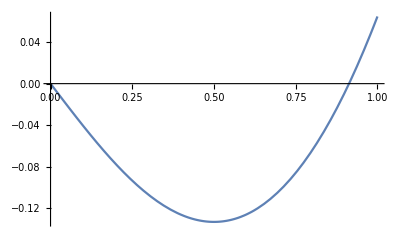

```mathematica
Plot[1/4 (-4 √2 x+2 x √(1+4 x^2)+ArcSinh[2 x]),{x,0,1}]
```

```mathematica
x y 3-x
```

-x+3 x y

```mathematica
Plot3D[-x+3 x y,{x,-8,8},{y,-8,8}]
```

-Graphics3D-

```mathematica
y-x^2==0
```

-x^2+y==0

```mathematica
y-x^2
```

-x^2+y

```mathematica
Plot3D[-x^2+y,{x,-2.2882456112707374,2.2882456112707374},{y,-6.,6.}]
```

-Graphics3D-

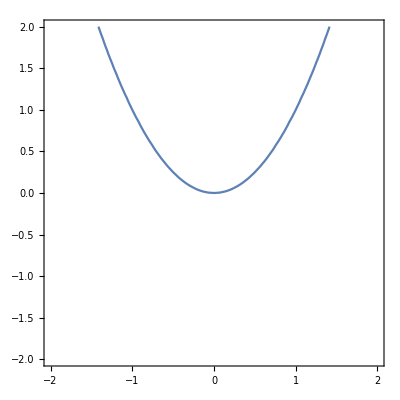

```mathematica
ContourPlot[-x^2+y==0,{x,-2,2},{y,-2,2}]
```

```mathematica
Plot3D[{0,-x^2+y},{x,-2.2882456112707374,2.2882456112707374},{y,-6.,6.}]
```

-Graphics3D-

```mathematica
Plot3D[{0,-x^2+y},{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Show[{
Plot3D[{0,-x^2+y},{x,-2,2},{y,-2,2}],
ParametricPlot3D[{t,t^2,0},{t,-2,2}]
}]
```

-Graphics3D-